# ECUACIONES DIFERENCIALES

## Segundo orden con coeficientes constantes:

Dr. Jorge Chávez Carlos

Es posible graficar un campo vectorial usando el comando:

VectorPlot[{v_x,v_y},{x,x_min,x_max},{y,y_min,y_max}]

Es de interes en un sistema de ecuaciones diferenciales graficar el espacio fase, con el sistema de ecuaciones dado como:

x'=ax+by
y'=cx+dy

Por lo tanto para graficar el espacio fase del sistema de ecuaciones se escribe:

VectorPlot[{a x+b y,c x+ d y},{x,x_min,x_max},{y,y_min,y_max}]

## Ejemplo 1:

Introduce el valor de los valores  “a, b, c, d” una vez introducidos

```mathematica
a=2;
b=-5;
c=1;
d=-2;
```

```mathematica
A={{0,1},{-c/a,-b/a}};
A//MatrixForm
```

(0 | 1
-c/a | -b/a)

```mathematica
li=Eigenvalues[A]
vi=Eigenvectors[A]
```

{(-b-√(b^2-4 a c))/(2 a),(-b+√(b^2-4 a c))/(2 a)}

{{-(b-√(b^2-4 a c))/(2 c),1},{-(b+√(b^2-4 a c))/(2 c),1}}

```mathematica
P={{1,-(b-√(b^2-4 a c))/(2 c)},{1,-(b+√(b^2-4 a c))/(2 c)}}
```

{{1,-(b-√(b^2-4 a c))/(2 c)},{1,-(b+√(b^2-4 a c))/(2 c)}}

una vez introducidos ejecuta la siguiente linea :

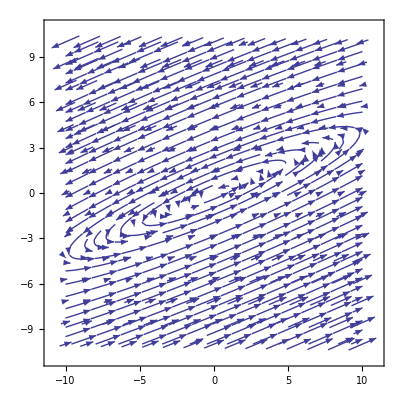

```mathematica
VectorPlot[{a x+b y,c x+d y},{x,-10,10},{y,-10,10},StreamPoints-> Fine,Axes->True]
```

## Ejemplo 2:

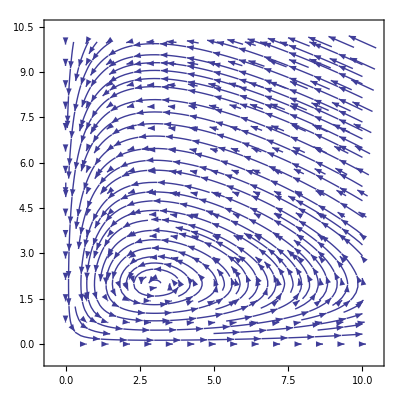

```mathematica
VectorPlot[{1x-.5x y,-0.75y+.25x y},{x,0,10},{y,0,10},StreamPoints-> Fine]
```